```mathematica
Integrate[mu*E^(e/T)/((E^(e/T)+1)^2*T)*e^2,{e,0,Infinity}]
```

ConditionalExpression[1/6 mu π^2 T^2,(Re[(-1)^T]≥1||Re[(-1)^T]≤0||(-1)^T∉Reals)&&Re[T]>0]

```mathematica
Integrate[mu*E^(e/T)/((E^(e/T)-1)^2*T)*e^2,{e,0,Infinity}]
```

ConditionalExpression[1/3 mu π^2 T^2,Re[T]>0]

```mathematica
Series[1/(E^((e-mu)/T)+1),{mu,0,1}]
```

1/(1+ⅇ^(e/T))+(ⅇ^(e/T) mu)/((1+ⅇ^(e/T))^2 T)+O[mu]^2

```mathematica
Integrate[ⅇ^(e/T)/((-1+ⅇ^(e/T))^2)*e^2,{e,0,Infinity}]
```

ConditionalExpression[(π^2 T^3)/3,Re[T]>0]

```mathematica
Rasterize[LogLogPlot[{z^2,3/Pi^2*(1+1/3)z^4*BesselK[1,z],3/Pi^2*(344/537+26/179)z^4*BesselK[1,z]},{z,1,10},PlotRange-> {0.005,100},PlotLegends -> {Subscript[Γ,N],
"Γ_(B - L); T>>10^13GeV","Γ_(B - L); 10^11GeV>T>10^8GeV"},Frame->{{True,False},{True,False}},FrameLabel->{{"K^-1 (Γ/H)",None},{"z",None}},FrameTicks->All],ImageResolution->{200}]
```

Thread::tdlen: Objects of unequal length in {1249,464} {0.36} cannot be combined.

Set::shape: Lists {System`ConvertersDump`width$3728,System`ConvertersDump`height$3728} and {0.36} {1249,464} are not the same shape.

-Graphics-

3

2

2 2^(2/3) (3 π)^(1/3)

100

80

33/8+3 ((3 π)/2)^(2/3)

40/(√(33/8+3 ((3 π)/2)^(2/3)))

11.7661

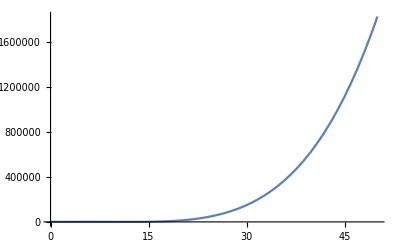

```mathematica
b=3
λ=2
g=(96Pi)^(1/3)
Subscript[m, t]=100
Subscript[m, H]=80
a=3/16*g^2+(1/2+Subscript[m, t]^2/Subscript[m, H]^2)*λ
Subscript[T, 1]=Subscript[m, H]/(2Sqrt[a])
T=11.76605407
Plot[1/2*a*(T^2-Subscript[T, 1]^2)x^2-1/3*b*T*x^3+1/4*λ*x^4,{x,0,50}]
```

```mathematica
Rasterize[Plot[{1/2*a*(25^2-Subscript[T, 1]^2)x^2-1/3*b*T*x^3+1/4*λ*x^4,1/2*a*(15^2-Subscript[T, 1]^2)x^2-1/3*b*T*x^3+1/4*λ*x^4,1/2*a*(11.76605407^2-Subscript[T, 1]^2)x^2-1/3*b*T*x^3+1/4*λ*x^4,1/2*a*(9^2-Subscript[T, 1]^2)x^2-1/3*b*T*x^3+1/4*λ*x^4},{x,0,50},PlotLegends->{"T>>T_c","T>T_c","T=T_c","T<T_c"},Ticks->None, AxesLabel-> {ϕ,Subscript[V, eff]},
AxesStyle->Arrowheads[0.02]],
ImageResolution->200]
```

-Graphics-

7

2

2 2^(2/3) (3 π)^(1/3)

100

80

33/8+3 ((3 π)/2)^(2/3)

40/(√(33/8+3 ((3 π)/2)^(2/3)))

15

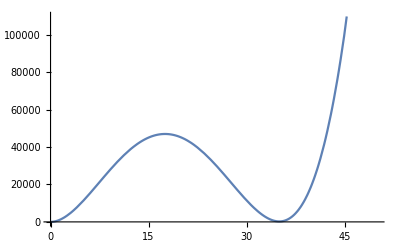

```mathematica
b=7
λ=2
g=(96Pi)^(1/3)
Subscript[m, t]=100
Subscript[m, H]=80
a=3/16*g^2+(1/2+Subscript[m, t]^2/Subscript[m, H]^2)*λ
Subscript[T, 1]=Subscript[m, H]/(2Sqrt[a])
T=15
Plot[1/2*a*(T^2-Subscript[T, 1]^2)x^2-1/3*b*T*x^3+1/4*λ*x^4,{x,0,50}]
```

```mathematica
Rasterize[Plot[{1/2*a*(20^2-Subscript[T, 1]^2)x^2-1/3*b*T*x^3+1/4*λ*x^4,1/2*a*(16^2-Subscript[T, 1]^2)x^2-1/3*b*T*x^3+1/4*λ*x^4,1/2*a*(15^2-Subscript[T, 1]^2)x^2-1/3*b*T*x^3+1/4*λ*x^4,1/2*a*(14.7^2-Subscript[T, 1]^2)x^2-1/3*b*T*x^3+1/4*λ*x^4},{x,0,50},PlotLegends->{"T>>T_c","T>T_c","T=T_c","T<T_c"},
AxesLabel-> {ϕ,Subscript[V, eff]},
AxesStyle->Arrowheads[0.02],
PlotRange->{-100000,100000},
Ticks->{{{35.0057705931649,"ϕ_c"}},None}],
ImageResolution->{200}]
```

Thread::tdlen: Objects of unequal length in {927,456} {0.36} cannot be combined.

Set::shape: Lists {System`ConvertersDump`width$8777,System`ConvertersDump`height$8777} and {0.36} {927,456} are not the same shape.

-Graphics-

```mathematica
Solve[D[1/2*a*(15^2-Subscript[T, 1]^2)x^2-1/3*b*T*x^3+1/4*λ*x^4]==0,x]
```

{{x→0},{x→0},{x→5/4 (28-√(2 (95-108 2^(1/3) (3 π)^(2/3)+2112/(33/8+3 ((3 π)/2)^(2/3))+(768 2^(1/3) (3 π)^(2/3))/(33/8+3 ((3 π)/2)^(2/3)))))},{x→5/4 (28+√(2 (95-108 2^(1/3) (3 π)^(2/3)+2112/(33/8+3 ((3 π)/2)^(2/3))+(768 2^(1/3) (3 π)^(2/3))/(33/8+3 ((3 π)/2)^(2/3)))))}}

```mathematica
5/4 (28+√(2 (95-108 2^(1/3) (3 π)^(2/3)+2112/(33/8+3 ((3 π)/2)^(2/3))+(768 2^(1/3) (3 π)^(2/3))/(33/8+3 ((3 π)/2)^(2/3)))))
```

5/4 (28+√(2 (95-108 2^(1/3) (3 π)^(2/3)+2112/(33/8+3 ((3 π)/2)^(2/3))+(768 2^(1/3) (3 π)^(2/3))/(33/8+3 ((3 π)/2)^(2/3)))))

```mathematica
N[5/4 (28+√(2 (95-108 2^(1/3) (3 π)^(2/3)+2112/(33/8+3 ((3 π)/2)^(2/3))+(768 2^(1/3) (3 π)^(2/3))/(33/8+3 ((3 π)/2)^(2/3)))))]
```

35.+0.63559 ⅈ

```mathematica
Abs[35.+0.6355901362422344 ⅈ]
```

35.0058